## Линейный конгруэнтный генератор

```mathematica
nMax=1000;
mod = 2^8;
(*lc[m_,a_,c_,x_]:=,*)
lkp[m_,a_,c_,x_]:=RecurrenceTable[
{X[n+1]==Mod[(a*X[n]+c),m],X[1]==x},
X,
{n,1,nMax}
];
t = Table[{ListPlot[lkp[mod,a,c,0]], a,c}, {a,27,47,1},{c,1,20,3}];
```

```mathematica
lkp[mod,9,13,0];
```

### Графики последовательностей с разными начальным значением

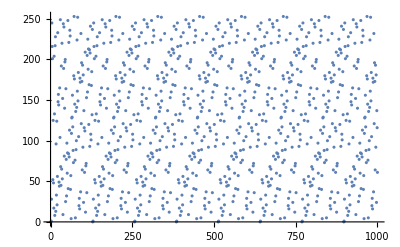
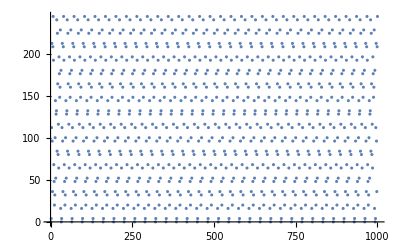
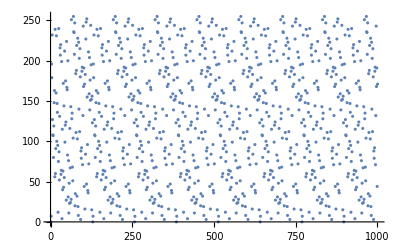
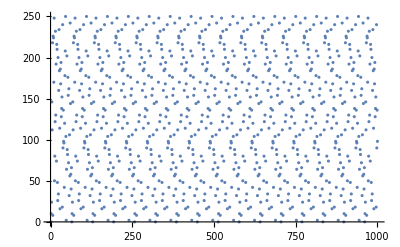
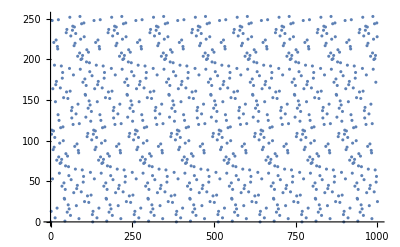
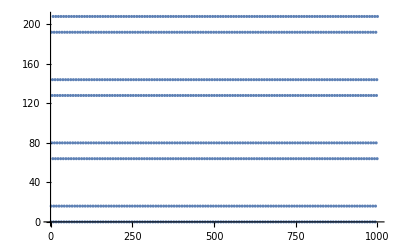
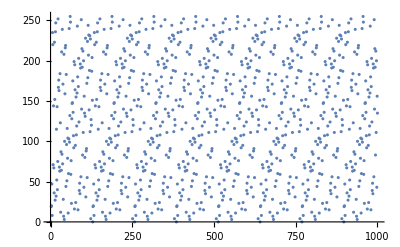
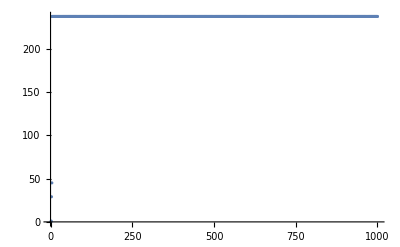
{{{-Graphics-,27,1},{-Graphics-,27,4},{-Graphics-,27,7},{-Graphics-,27,10},{-Graphics-,27,13},{-Graphics-,27,16},{-Graphics-,27,19}},{{-Graphics-,28,1},{-Graphics-,28,4},{-Graphics-,28,7},{-Graphics-,28,10},{-Graphics-,28,13},{-Graphics-,28,16},{-Graphics-,28,19}},{{-Graphics-,29,1},{-Graphics-,29,4},{-Graphics-,29,7},{-Graphics-,29,10},{-Graphics-,29,13},{-Graphics-,29,16},{-Graphics-,29,19}},{{-Graphics-,30,1},{-Graphics-,30,4},{-Graphics-,30,7},{-Graphics-,30,10},{-Graphics-,30,13},{-Graphics-,30,16},{-Graphics-,30,19}},{{-Graphics-,31,1},{-Graphics-,31,4},{-Graphics-,31,7},{-Graphics-,31,10},{-Graphics-,31,13},{-Graphics-,31,16},{-Graphics-,31,19}},{{-Graphics-,32,1},{-Graphics-,32,4},{-Graphics-,32,7},{-Graphics-,32,10},{-Graphics-,32,13},{-Graphics-,32,16},{-Graphics-,32,19}},{{-Graphics-,33,1},{-Graphics-,33,4},{-Graphics-,33,7},{-Graphics-,33,10},{-Graphics-,33,13},{-Graphics-,33,16},{-Graphics-,33,19}},{{-Graphics-,34,1},{-Graphics-,34,4},{-Graphics-,34,7},{-Graphics-,34,10},{-Graphics-,34,13},{-Graphics-,34,16},{-Graphics-,34,19}},{{-Graphics-,35,1},{-Graphics-,35,4},{-Graphics-,35,7},{-Graphics-,35,10},{-Graphics-,35,13},{-Graphics-,35,16},{-Graphics-,35,19}},{{-Graphics-,36,1},{-Graphics-,36,4},{-Graphics-,36,7},{-Graphics-,36,10},{-Graphics-,36,13},{-Graphics-,36,16},{-Graphics-,36,19}},{{-Graphics-,37,1},{-Graphics-,37,4},{-Graphics-,37,7},{-Graphics-,37,10},{-Graphics-,37,13},{-Graphics-,37,16},{-Graphics-,37,19}},{{-Graphics-,38,1},{-Graphics-,38,4},{-Graphics-,38,7},{-Graphics-,38,10},{-Graphics-,38,13},{-Graphics-,38,16},{-Graphics-,38,19}},{{-Graphics-,39,1},{-Graphics-,39,4},{-Graphics-,39,7},{-Graphics-,39,10},{-Graphics-,39,13},{-Graphics-,39,16},{-Graphics-,39,19}},{{-Graphics-,40,1},{-Graphics-,40,4},{-Graphics-,40,7},{-Graphics-,40,10},{-Graphics-,40,13},{-Graphics-,40,16},{-Graphics-,40,19}},{{-Graphics-,41,1},{-Graphics-,41,4},{-Graphics-,41,7},{-Graphics-,41,10},{-Graphics-,41,13},{-Graphics-,41,16},{-Graphics-,41,19}},{{-Graphics-,42,1},{-Graphics-,42,4},{-Graphics-,42,7},{-Graphics-,42,10},{-Graphics-,42,13},{-Graphics-,42,16},{-Graphics-,42,19}},{{-Graphics-,43,1},{-Graphics-,43,4},{-Graphics-,43,7},{-Graphics-,43,10},{-Graphics-,43,13},{-Graphics-,43,16},{-Graphics-,43,19}},{{-Graphics-,44,1},{-Graphics-,44,4},{-Graphics-,44,7},{-Graphics-,44,10},{-Graphics-,44,13},{-Graphics-,44,16},{-Graphics-,44,19}},{{-Graphics-,45,1},{-Graphics-,45,4},{-Graphics-,45,7},{-Graphics-,45,10},{-Graphics-,45,13},{-Graphics-,45,16},{-Graphics-,45,19}},{{-Graphics-,46,1},{-Graphics-,46,4},{-Graphics-,46,7},{-Graphics-,46,10},{-Graphics-,46,13},{-Graphics-,46,16},{-Graphics-,46,19}},{{-Graphics-,47,1},{-Graphics-,47,4},{-Graphics-,47,7},{-Graphics-,47,10},{-Graphics-,47,13},{-Graphics-,47,16},{-Graphics-,47,19}}}

```mathematica
t
```